```mathematica
Efunc[μ_,Γ_,a_,x_]:=ⅇ^(-x^2/(2μ))∑_(s=-∞)^∞ DiracDelta[x-(s+a)Γ];
Efunct[μ_,Γ_,a_,x_]:=ⅇ^(-x^2/(2μ))∑_(s=-∞)^∞ ⅇ^(2π ⅈ a s)DiracDelta[x-s Γ];
Gauss[v_,x_]:=1/(√(2π v))ⅇ^(-x^2/(2v));
Θ[a_,b_,z_,τ_]:=Exp[π ⅈ τ a^2 + 2π ⅈ a (z+b)]EllipticTheta[3,π(z+ τ a + b), Exp[π ⅈ τ]];
αd[d_]:=√((2π)/d);
Λ[vq_,vp_]:=1-4vq vp;
norm[vq_,vp_,Γ_,j_,d_]:=Re[Θ[j/d,0,0,(2ⅈ Γ^2)/π  vp^2/Λ[vq,vp]]Θ[0,0,0, (2π ⅈ)/Γ^2 vq^2/Λ[vq,vp]]+Θ[j/d+1/2,0,0,(2ⅈ Γ^2)/π  vp^2/Λ[vq,vp]]Θ[0,1/2,0, (2π ⅈ)/Γ^2 vq^2/Λ[vq,vp]]];
```

```mathematica
EconvG[μ_,Γ_,a_,v_,x_]:= Gauss[v,x]Θ[a,0,(Γ x)/(2 π ⅈ v),(ⅈ Γ^2 (1+v/μ))/(2 π v)];

EtconvG[μ_,Γ_,a_,v_,x_]:= Gauss[v,x]Θ[0,a,(ⅈ Γ x)/(2 π v),(ⅈ Γ^2)/(2 π v)];
```

Note : σ^2 = 0.5 means 0 squeezing so 0 < σ^2 (variance) < 0.5

```mathematica
ProductTerm[q_,p_,d_,i_,j_,vq_,vp_,Γ_,parity_]:=Chop[EconvG[Λ[vq,vp]/(4vp),Γ,(i+j)/(2d)+parity/2,vq,q]]Chop[EtconvG[Λ[vq,vp]/(4vq),(π Λ[vq,vp])/Γ,(i-j)/(2d)+parity/2,vp,p]];
Wigner[q_,p_,d_,i_,j_,vq_,vp_,Γ_]:=1/(√(norm[vq,vp,Γ,i,d]norm[vq,vp,Γ,j,d]))Chop[ProductTerm[q,p,d,i,j,vq,vp,Γ,0]+ProductTerm[q,p,d,i,j,vq,vp,Γ,1]];
(* Wigner for vacuum *)
Vacner[q_,p_]:= 1/(2π)ⅇ^(-1/2(q^2+p^2));

(* After beamsplitter given Bololiubov B = {{t, ⅈ r},{ⅈ r, t}} with t = √η *)
 (* The quadratures will mix according to {q1,p1,q2,p2} as {{t,0,0,-r},{0,t,r,0},{0,-r,t,0},{r,0,0,t}} *)

B[t_,r_]:= {{t,0,0,-r},{0,t,r,0},{0,-r,t,0},{r,0,0,t}};
B[t,r].{q1,p1,q2,p2}//MatrixForm
```

(-p2 r+q1 t
q2 r+p1 t
-p1 r+q2 t
q1 r+p2 t)

```mathematica
WignerAfterBS[t_,r_,q1_,p1_,q2_,p2_,d_,i_,j_,vq_,vp_,Γ_]:=Wigner[(B[t,r].{q1,p1,q2,p2})[[1]],(B[t,r].{q1,p1,q2,p2})[[2]],d,i,j,vq,vp,Γ]Vacner[(B[t,r].{q1,p1,q2,p2})[[3]],(B[t,r].{q1,p1,q2,p2})[[4]]];
```

## Tracing over mode 2

```mathematica
WignerAfterLoss[t_,r_,q1_,p1_,d_,i_,j_,vq_,vp_,Γ_]:=∫_(-∞)^∞ ∫_(-∞)^∞ WignerAfterBS[t,r,q1,p1,x,y,d,i,j,vq,vp,Γ]ⅆxⅆy;
```

```mathematica
WignerAfterLoss[√0.75,√(1-0.75),0,0,d,0,0,vq,vp,Γ]
```

∫_(-∞)^∞ ⅇ^(-2.875 x^2) ((0.0000338064-2.23937×10^-19 ⅈ) EllipticTheta[3,1.5708+(0.+4.40892 ⅈ) x,0.000419922]+0.00267461 EllipticTheta[3,(0.+4.40892 ⅈ) x,0.000419922])ⅆx

```mathematica
ClearAll[mat,limits,range,vq,vp,d,Γ];
limits=2;
range=60;
vq = vp = 0.05;
d=2;
Γ =αd[d] d √Λ[vq,vp];
Δ= 0.05;
η=0.75;

(* List Desnity Plot - fast *) 
Quiet[
mat=Table[Re[Chop[WignerAfterLoss[√η,√(1-η),√π((x-1)(limits/range)-limits),√π((p-1)(limits/range)-limits),d,0,0,vq,vp,Γ]]],{p,1,2 range +1},{x,1,2 range +1}];
];
mat=mat/(1+0Abs[Total[mat,2]](limits/range)^2);

plot=ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]
```

-Graphics-

## Heterodyne on mode 2

```mathematica
Heterodyne[t_,r_,q1_,p1_,q2_,p2_,d_,i_,j_,vq_,vp_,Γ_]:=∫_(-∞)^∞ ∫_(-∞)^∞ Vacner[q2-x,p2-y]WignerAfterBS[t,r,q1,p1,x,y,d,i,j,vq,vp,Γ]ⅆxⅆy;
```

For symmetric case vq=vp=v, Γ = α_d d √Λ (Section 5. from Ref.)

```mathematica
ClearAll[mat,limits,range,vq,vp,d,Γ];
limits=2;
range=60;
vq = vp = 0.05;
d=2;
Γ =αd[d] d √Λ[vq,vp];
Δ= 0.05;
η=0.75;
WignerAfterBS[√η,√(1-η),0,0,0,0,d,0,0,vq,vp,Γ]
```

```mathematica
Heterodyne[t_,r_,q1_,p1_,q2_,p2_,d_,i_,j_,vq_,vp_,Γ_]:=NIntegrate[Vacner[q2-x,p2-y]WignerAfterBS[t,r,q1,p1,x,y,d,i,j,vq,vp,Γ],{x,-50 √π,50 √π},{y,-50 √π,50 √π}]
```

```mathematica
AfterHeterodyne[Δ_,t_,r_,q1_,p1_,d_,i_,j_,vq_,vp_,Γ_]:=NIntegrate[Heterodyne[t,r,q1,p1,q2,p2,d,i,j,vq,vp,Γ],{q2,-Δ/2,Δ/2},{p2,-Δ/2,Δ/2}];
```

```mathematica
Plot3D[NIntegrate[Vacner[q2-x,p2-y]WignerAfterBS[√η,√(1-η),0,0,x,y,d,0,0,vq,vp,Γ],{x,-2,2},{y,-2,2}],{q2,-5,5},{p2,-5,5},PlotRange->All,PlotPoints->10,Mesh->None,ColorFunction->(Blend[{Blue,White,Red},#3]&),ColorFunctionScaling->True]
```

-Graphics3D-

```mathematica
NIntegrate[Vacner[q2-x,p2-y]WignerAfterBS[√η,√(1-η),1,1,x,y,d,0,0,vq,vp,Γ],{x,-1000π,1000 √π},{y,-1000 √π,10 √π},{q2,-1/10 √π,1/10 √π},{p2,-1/10 √π,1/10 √π}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
Vacner[q2-x,p2-y]
```

(ⅇ^(1/2 (-(q2-x)^2-(p2-y)^2)))/(2 π)

```mathematica
Heterodyne[√η,√(1-η),0,0,0,0,d,0,0,vq,vp,Γ]
```

0.000480297

```mathematica
AfterHeterodyne[10 √π,√η,√(1-η),0,0,d,0,0,vq,vp,Γ]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

0.00256076

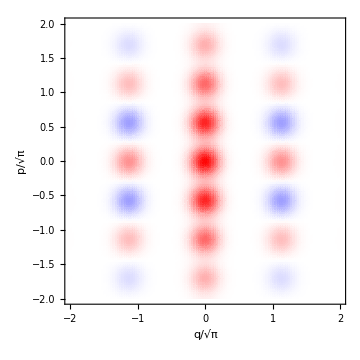

```mathematica
(* List Desnity Plot - fast *) 
Quiet[
mat=Table[Re[Chop[WignerAfterBS[√η,√(1-η),√π((x-1)(limits/range)-limits),√π((p-1)(limits/range)-limits),0,0,d,0,0,vq,vp,Γ]]],{p,1,2 range +1},{x,1,2 range +1}];
];
mat=mat/(1+0Abs[Total[mat,2]](limits/range)^2);

plot=ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]
```

```mathematica
Heterodyne[√η,√(1-η),0,0,0,0,d,0,0,vq,vp,Γ]
```

$Aborted

```mathematica
(* Density Plot - slow *)
Quiet[DensityPlot[Wigner[√π(q),√π(p),d,1,1,vq,vp,Γ],{q,-limits,limits},{p,-limits,limits},PlotPoints->60,ColorFunction->(Blend[{Blue,White,Red},(π*#+1)/2]&),ColorFunctionScaling->False,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]]
```

```mathematica
(* List Desnity Plot - fast *) 
Quiet[
mat=Table[Re[Chop[Wigner[√π((x-1)(limits/range)-limits),√π((p-1)(limits/range)-limits),d,0,0,vq,vp,Γ]]],{p,1,2 range +1},{x,1,2 range +1}];
];
mat=mat/(1+0Abs[Total[mat,2]](limits/range)^2);
```

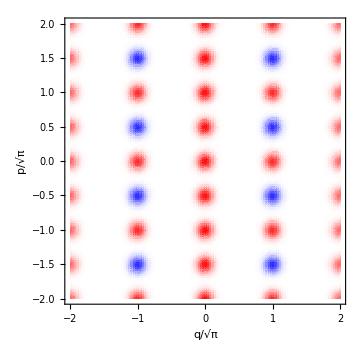

```mathematica
plot=ListDensityPlot[mat,DataRange->{{-limits,limits},{-limits,limits}},ColorFunction->(Blend[{Blue,White,Red},(#/Max[{Abs[Max[mat]],Abs[Min[mat]]}]+1)/2]&),ColorFunctionScaling->False,PlotRange->All,LabelStyle->{FontSize->Medium,FontFamily->"Arial",Black},AxesStyle->{Thick,Black},ImageSize->Medium,FrameLabel->{"q/√π","p/√π"}]
```

```mathematica
ClearAll[mat,limits,range,vq,vp,d,Γ];
```